# Outer Products for Matrix Multiplication

## Technical Report, GSI Technology

Brian Beckman
Technology Fellow
November, 2023

## Abstract

Accumulated outer products are much faster than iterated inner products for matrix multiplication.

## Iterated Inner Product Versus Accumulated Outer Product

### Set Up

Set some array dimensions as mutually co-prime numbers, for generality.

Consider a small matrix of floating-point numbers in the range [0., 1.], inclusive both ends.

```mathematica
ClearAll[m,n,k,A,B];
m=5;k=4;n=7;GCD[m,k,n]
(A=RandomReal[{0.,1.},{m,k}])//MatrixForm
```

1

(0.890357 | 0.306668 | 0.72266 | 0.239548
0.844541 | 0.570467 | 0.986809 | 0.787673
0.047082 | 0.127307 | 0.532343 | 0.293322
0.140779 | 0.643162 | 0.867441 | 0.374358
0.693865 | 0.191579 | 0.80286 | 0.76817)

Natively, A is a List of rows with two levels of brackets. Indexing A yields a row vector, with only one level of brackets.

```mathematica
A[[2]]
```

{0.844541,0.570467,0.986809,0.787673}

To get a column of A, transpose a row of the transpose. Again, the result has only one level of brackets, so its type as a column vector is implicit. It has exactly the same shape as a row vector. This ambiguity is a defect, however, it is commonplace in programming languages.

```mathematica
Aᵀ[[2]]ᵀ
```

{0.306668,0.570467,0.127307,0.643162,0.191579}

Write a couple of more explicit helper functions.

```mathematica
ClearAll[row,col];
row[M_,i_]:=M[[i]];
col[M_,i_]:=Mᵀ[[i]]ᵀ;
```

Make another matrix to play with.

```mathematica
(B=RandomReal[{0.,1.},{k,n}])//MatrixForm
```

(0.566316 | 0.280131 | 0.172263 | 0.864077 | 0.988026 | 0.764716 | 0.367914
0.0143118 | 0.439713 | 0.307832 | 0.0901381 | 0.685131 | 0.742714 | 0.781634
0.0413802 | 0.0337941 | 0.421831 | 0.767083 | 0.958825 | 0.156234 | 0.0270575
0.195809 | 0.434148 | 0.247417 | 0.288402 | 0.877875 | 0.285469 | 0.250479)

Check Mathematica’s built-in matrix product.

```mathematica
(A.B)//MatrixForm
```

(0.585422 | 0.512683 | 0.611886 | 1.42041 | 1.993 | 1.08992 | 0.646832
0.681509 | 0.862739 | 0.932241 | 1.7653 | 2.86293 | 1.44856 | 0.980611
0.107949 | 0.214503 | 0.344431 | 0.545104 | 0.901664 | 0.297461 | 0.204704
0.198127 | 0.514084 | 0.680772 | 0.952982 | 1.74011 | 0.827732 | 0.671751
0.579326 | 0.639244 | 0.707231 | 1.45422 | 2.26097 | 1.01762 | 0.619161)

### Iterated Inner Product

Iterate inner products -- a school algorithm -- row vectors times column vectors. The following shows row 2 of A inner-product col 2 of B to produce element (2,2) of the product A.B.

```mathematica
row[A,2].col[B,2]
```

0.862739

Here is iterated inner product compared for accuracy against the built-in, intrinsic matrix product.

```mathematica
On[Assert];
```

```mathematica
Assert[Module[{i,j,ab=ConstantArray[0.0,{m,n}]},
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];
ab]===A.B]
```

### Accumulated Outer Product

Check outer product:

```mathematica
Outer[Times,col[A,2],row[B,2]]//MatrixForm
```

(0.00438898 | 0.134846 | 0.0944021 | 0.0276424 | 0.210108 | 0.227766 | 0.239702
0.00816443 | 0.250842 | 0.175608 | 0.0514208 | 0.390845 | 0.423694 | 0.445896
0.00182199 | 0.0559784 | 0.0391891 | 0.0114752 | 0.0872218 | 0.0945525 | 0.0995073
0.00920483 | 0.282807 | 0.197986 | 0.0579734 | 0.44065 | 0.477686 | 0.502717
0.00274184 | 0.0842396 | 0.058974 | 0.0172685 | 0.131256 | 0.142288 | 0.149744)

Here is matrix product as accumulated outer product compared against the built-in, intrinsic matrix product. Notice there is only one loop, so this outer-product algorithm should be much faster than the iterated inner-product.

```mathematica
Assert[Module[{kk,ab=ConstantArray[0.0,{m,n}]},
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];
ab]===A.B]
```

### Helper Functions

Even with these very small matrices, the accumulated outer product is much faster than the iterated inner product.

```mathematica
ClearAll[iteratedInnerProduct,accumulatedOuterProduct,builtInProduct];
iteratedInnerProduct[m_,k_,n_,A_,B_]:=
Module[{i,j,ab=ConstantArray[0.0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[i=1,i<=m,i++,
For[j=1,j<=n,j++,
ab[[i,j]]=row[A,i].col[B,j]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
accumulatedOuterProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab=ConstantArray[0.0,{m,n}],result,time},
{time,result}=AbsoluteTiming[
For[kk=1,kk<=k,kk++,
ab+=Outer[Times,col[A,kk],row[B,kk]]];ab];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
builtInProduct[m_,k_,n_,A_,B_]:=
Module[{kk,ab,result,time},
{time,result}=AbsoluteTiming[ab=A.B];
<|"m"->m,"k"->k,"n"->n,"result"->result,
"time"->Quantity[time,"Seconds"]|>];
With[{ab=builtInProduct[m,k,n,A,B],
abi=iteratedInnerProduct[m,k,n,A,B],
aba=accumulatedOuterProduct[m,k,n,A,B]},
Assert[ab["result"]===abi["result"]===aba["result"]];
Print[<|"built-in time"->ab["time"],
"inner time"->abi["time"],"outer time"->aba["time"],
"inner/outer ratio"->N[abi["time"]/aba["time"]],
"outer/built-in ratio"->N[aba["time"]/ab["time"]]|>];]
```

<|built-in time→1.×10^-6 s,inner time→0.000093 s,outer time→0.000016 s,inner/outer ratio→5.8125,outer/built-in ratio→16.|>

### Large Matrices

With the following dimensions, iterated inner product takes 20 minutes: too long to wait.

```mathematica
GCD[1001,1114,993]
```

1

```mathematica
ClearAll[timings];
(timings=With[{precision=1.*^-5},
Module[{timings=
Table[With[{m=d,k=d,n=d},
With[{A=RandomReal[{0.,1.},{m,k}],
B=RandomReal[{0.,1.},{k,n}]},
<|"dim"->d,
"built-in"->builtInProduct[m,k,n,A,B],
"inner"->iteratedInnerProduct[m,k,n,A,B],
"outer"->accumulatedOuterProduct[m,k,n,A,B]|>
]],{d,1,400,25}]},
Map[Assert[
Round[#["built-in"]["result"],precision]===
Round[#["inner"]["result"],precision]===
Round[#["outer"]["result"],precision]
]&,timings];
Map[{#["dim"],#["built-in"]["time"],#["inner"]["time"],#["outer"]["time"]}&,timings]
]])//MatrixForm
```

(1 | 6.×10^-6 s | 7.×10^-6 s | 5.×10^-6 s
26 | 0.000015 s | 0.001736 s | 0.000081 s
51 | 0.000014 s | 0.008294 s | 0.000236 s
76 | 0.000862 s | 0.030495 s | 0.000655 s
101 | 0.002773 s | 0.062347 s | 0.001334 s
126 | 0.000094 s | 0.111895 s | 0.002427 s
151 | 0.000257 s | 0.193579 s | 0.003802 s
176 | 0.00026 s | 0.27655 s | 0.004654 s
201 | 0.000169 s | 0.310438 s | 0.004638 s
226 | 0.000195 s | 0.96837 s | 0.012266 s
251 | 0.000449 s | 1.24754 s | 0.009841 s
276 | 0.000399 s | 1.10172 s | 0.00947 s
301 | 0.000409 s | 1.55633 s | 0.012852 s
326 | 0.000439 s | 1.84764 s | 0.012872 s
351 | 0.000559 s | 2.28219 s | 0.018301 s
376 | 0.000682 s | 2.5385 s | 0.020523 s)

```mathematica
ClearAll[plottableTimings];
plottableTimings[j_]:={col[timings,1],(Log10@*QuantityMagnitude)[col[timings,j]]}ᵀ
```

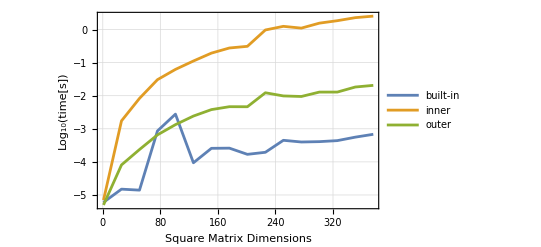

```mathematica
ListLinePlot[{plottableTimings[2],
plottableTimings[3],plottableTimings[4]},
(*ImageSize->Large,*)GridLines->Automatic,
Frame->True,PlotLegends->{"built-in","inner","outer"},
FrameLabel->{{"Log_10(time[s])",""},{"Square Matrix Dimensions","Running Times"}}]
```